# KL Distance Analysis

## Functional form of m_x

```mathematica
mparams={1.7,0.97};
```

### m_x

```mathematica
mx[t,mparams]
```

mx[t,{1.7,0.97}]

```mathematica
mx[t,mparams[[1]],mparams[[2]]]
```

mx[t,1.7,0.97]

mu2 Coth[5 mu1] Tanh[mu1 (-5+t)]

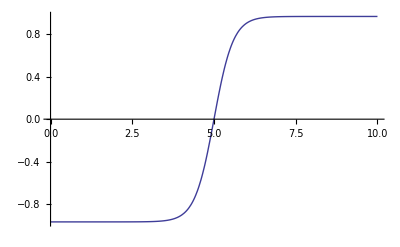

```mathematica
mx[t_,{mu1_,mu2_}]=mu2/Tanh[5*mu1]*Tanh[mu1*(t-5)]
Plot[mx[t,mparams],{t,0,10}]
```

### dm_x/dmu_1

mu2 (-5+t) Coth[5 mu1] Sech[mu1 (-5+t)]^2-5 mu2 Csch[5 mu1]^2 Tanh[mu1 (-5+t)]

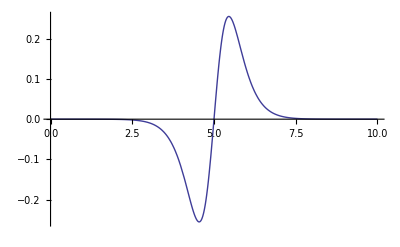

```mathematica
mxdmu1[t_,{mu1_,mu2_}]=D[mx[t,{mu1,mu2}],mu1]
Plot[mxdmu1[t,mparams],{t,0,10},PlotRange->All]
```

### dm_x/dmu_2

Coth[5 mu1] Tanh[mu1 (-5+t)]

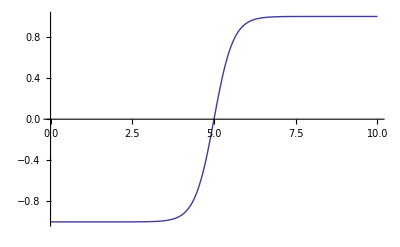

```mathematica
mxdmu2[t_,{mu1_,mu2_}]=D[mx[t,{mu1,mu2}],mu2]
Plot[mxdmu2[t,mparams],{t,0,10},PlotRange->All]
```

## Functional form of B_xx

```mathematica
Bparams={7.52,-1,3};
```

### Bxx

(s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))^2

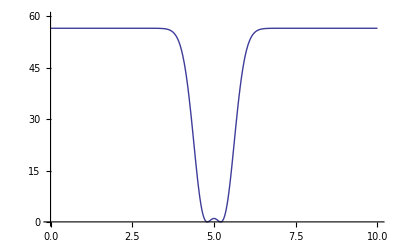

```mathematica
Bxx[t_,{s1_,s2_,s3_}]=(s1+(s2-s1)*Exp[-s3*(t-5.)^2])^2
Plot[Bxx[t,Bparams],{t,0,10},PlotRange->{{0,10},{0,60}}]
```

### dBxx/ds_1

2 (1-ⅇ^(-s3 (-5.+t)^2)) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))

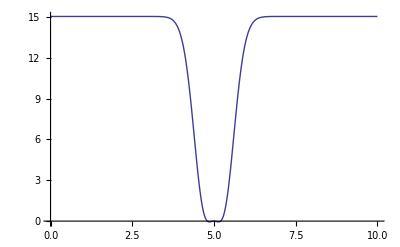

```mathematica
Bxxds1[t_,{s1_,s2_,s3_}]=D[Bxx[t,{s1,s2,s3}],s1]
Plot[Bxxds1[t,Bparams],{t,0,10},PlotRange->All]
```

### dBxx/ds_2

2 ⅇ^(-s3 (-5.+t)^2) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))

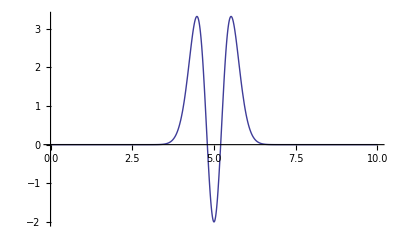

```mathematica
Bxxds2[t_,{s1_,s2_,s3_}]=D[Bxx[t,{s1,s2,s3}],s2]
Plot[Bxxds2[t,Bparams],{t,0,10},PlotRange->All]
```

### dBxx/ds_3

-2 ⅇ^(-s3 (-5.+t)^2) (-s1+s2) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2)) (-5.+t)^2

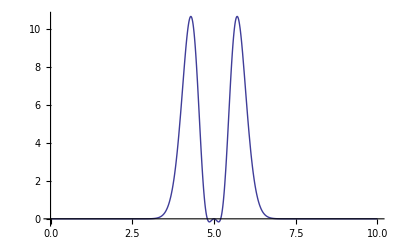

```mathematica
Bxxds3[t_,{s1_,s2_,s3_}]=D[Bxx[t,{s1,s2,s3}],s3]
Plot[Bxxds3[t,Bparams],{t,0,10},PlotRange->All]
```

## Simulation Data

```mathematica
data=Import["/mnt/heimdall/git/TwoDimTubes/BstpDesc/2WellTubes-T0.15-pos2000000.dat","Table"];
```

```mathematica
timedata=Table[i,{i,0,10,0.0005}];
```

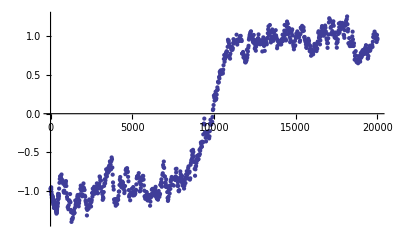

```mathematica
ListPlot[data[[All,1]],MaxPlotPoints->1000]
```

### dD_kl/dm

I-Iou= -8.90805

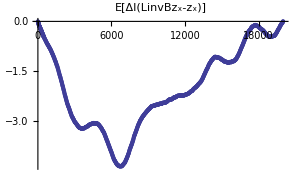

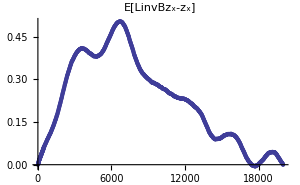

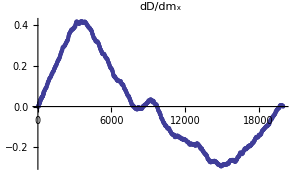

```mathematica
Print["I-Iou= "<>ToString[data[[1,9]]]]
ListPlot[data[[All,8]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[ΔI(LinvBz_x-z_x)]"]
ListPlot[data[[All,10]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[LinvBz_x-z_x]"]
ListPlot[data[[All,8+0]]-data[[All,8+1]]*data[[All,8+2]],PlotRange->All,MaxPlotPoints->1000,PlotLabel->"dD/dm_x"]
```

I-Iou= -8.90805

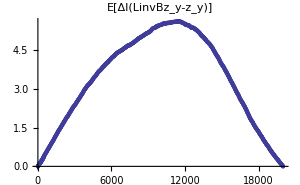

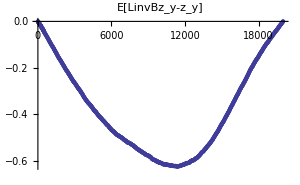

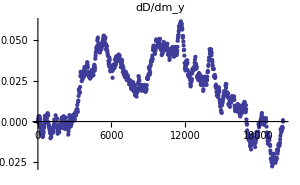

```mathematica
Print["I-Iou= "<>ToString[data[[1,12]]]]
ListPlot[data[[All,11]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[ΔI(LinvBz_y-z_y)]"]
ListPlot[data[[All,13]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[LinvBz_y-z_y]"]
ListPlot[data[[All,11+0]]-data[[All,11+1]]*data[[All,11+2]],PlotRange->All,MaxPlotPoints->1000,PlotLabel->"dD/dm_y"]
```

### dD_kl/dB_xx

I-Iou= -8.90805

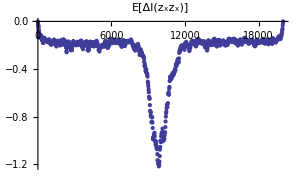

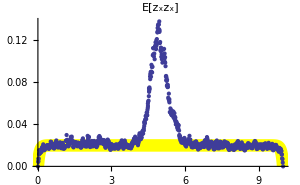

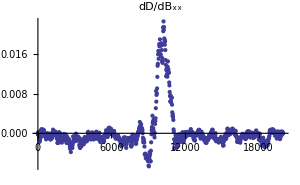

```mathematica
Print["I-Iou= "<>ToString[data[[1,15]]]]
ListPlot[data[[All,14]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300,PlotLabel->"E[ΔI(z_xz_x)]"]
Show[Plot[2 ϵ/A Sinh[A t] Sinh[A (T-t)]/Sinh[A T]/.{A->Bparams[[1]],ϵ->0.15,T->10},{t,0,10},PlotRange->All,PlotStyle->{Thickness[.03],Yellow},PlotLabel->"E[z_xz_x]"],ListPlot[Transpose[{timedata,data[[All,16]]}],PlotRange->All,MaxPlotPoints->1000,ImageSize->300]]
ListPlot[-data[[All,14+0]]+data[[All,14+1]]*data[[All,14+2]],PlotRange->All,MaxPlotPoints->1000,PlotLabel->"dD/dB_xx"]
```

dD_KL/dσ_2=∫dD/dB_xx dB_xx/dσ_2 du

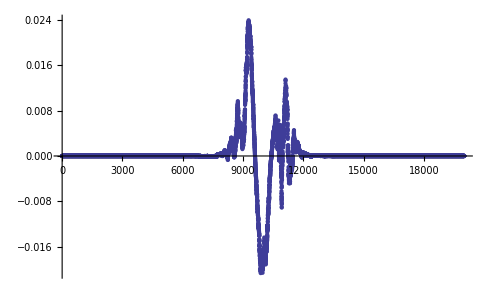

```mathematica
ListPlot[Table[Bxxds2[timedata[[i]],Bparams],{i,1,Length[timedata]}]*(-data[[All,14+0]]+data[[All,14+1]]*data[[All,14+2]]),PlotRange->All]
```

```mathematica
Table[Bxxds2[timedata[[i]],Bparams],{i,1,Length[timedata]}].(-data[[All,14+0]]+data[[All,14+1]]*data[[All,14+2]])
```

3.88913

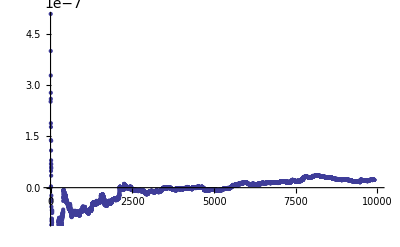
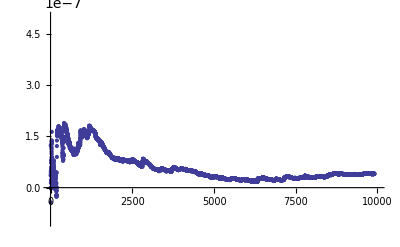
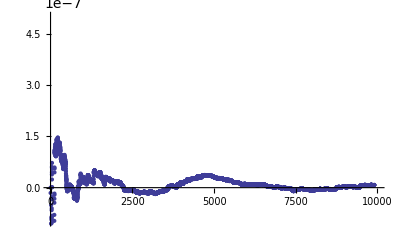
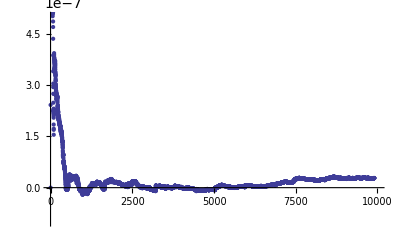
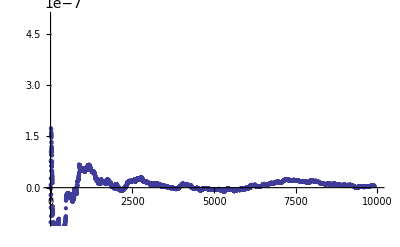
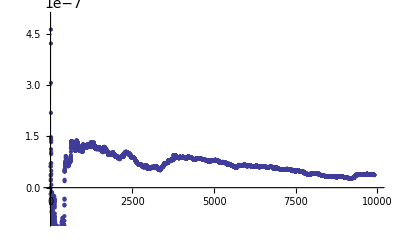
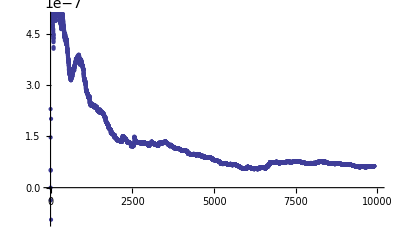
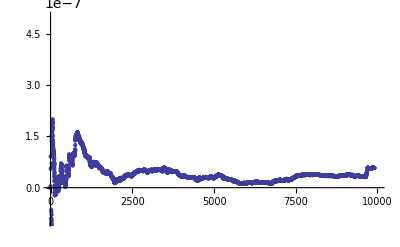

```mathematica
data1=Import["/home/patrick/git/TwoDimTubes/out10","Table"];
data2=Import["/home/patrick/git/TwoDimTubes/out15","Table"];
data3=Import["/home/patrick/git/TwoDimTubes/out20","Table"];
data4=Import["/home/patrick/git/TwoDimTubes/out25","Table"];
data5=Import["/home/patrick/git/TwoDimTubes/out30","Table"];
data6=Import["/home/patrick/git/TwoDimTubes/out35","Table"];
data7=Import["/home/patrick/git/TwoDimTubes/out40","Table"];
data8=Import["/home/patrick/git/TwoDimTubes/out45","Table"];
data9=Import["/home/patrick/git/TwoDimTubes/out50","Table"];
plotdata[datalist__,n_]:=((datalist[[23;;Length[datalist]-100]])/.{a1_,a2_,a3_,a4_,a5_,a6_}->a4)
Table[ListPlot[plotdata[ToExpression["data"<>ToString[i]],2],PlotRange->{{0,10000},{-10^-7,5*10^-7}}],{i,1,9}]
```